# Emprego da Frequência Complexa com Integração por Partes para Calcular a NLT

## parte 1: Visualização da respota em frequência

para comparação usando os resultados do artigo 20pwrd02gustavsen onde é usado frequência real

## Início

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Library/CloudStorage/Dropbox/[07]Codes/mma_codes

```mathematica
<<LineCableParam`
```

```mathematica
<<freqdomain`
```

```mathematica
(* Bright *)
bright={{Thick,Darker[Blue]},{Dashed,Thick,Darker[Red]},{DotDashed,Thick, Darker[Green]},{Thick, Darker[Yellow]},{Dashed,Thick, Darker[Cyan]},{Thick, DotDashed,Darker[Purple]},Darker[Gray]}
```

{{Thickness[Large],RGBColor[0, 0, Rational[2, 3]]},{Dashing[{Small,Small}],Thickness[Large],RGBColor[Rational[2, 3], 0, 0]},{Dashing[{0,Small,Small,Small}],Thickness[Large],RGBColor[0, Rational[2, 3], 0]},{Thickness[Large],RGBColor[Rational[2, 3], Rational[2, 3], 0]},{Dashing[{Small,Small}],Thickness[Large],RGBColor[0, Rational[2, 3], Rational[2, 3]]},{Thickness[Large],Dashing[{0,Small,Small,Small}],RGBColor[0.33333333333333337, 0, 0.33333333333333337]},RGBColor[0.33333333333333337, 0.33333333333333337, 0.33333333333333337]}

```mathematica
(* High Contrast *)
highContrast={Darker[Blue],Darker[Yellow], Darker[Red]};
```

```mathematica
(* Vibrant *)
vibrant={Darker[Orange],Darker[Blue],Darker[Cyan], Darker[Magenta],Darker[Red], Darker[Brown],Darker[Gray]};
```

```mathematica
SetOptions[{Plot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"TeX Gyre Termes", 14},PlotStyle-> bright,ImageSize-> 600,Frame->True,Axes->False];
```

```mathematica
SetOptions[{ListPlot, ListLogLogPlot, ListLogPlot,ListLogLinearPlot},BaseStyle->{FontFamily->"eX Gyre Termes", 14},PlotStyle-> bright,ImageSize-> 600,Frame->True,Joined->True,Axes->False];
```

para não reclamar dos valores de 0/0

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
```

## Funções adicionais

```mathematica
montaLap[m_,nn_]:=Module[{outlow=m,lowerhalf,upperhalf},
lowerhalf=Delete[outlow,nf];
upperhalf=Reverse[Conjugate[outlow]];
upperhalf=Delete[upperhalf,nf];Join[lowerhalf,upperhalf]]
```

```mathematica
nILT[F_,τ_,Δt_]:=Module[{nc},
nc=Dimensions[F][[2]];Table[Exp[c τ]/Δt Re[ InverseFourier[F[[All,i]] ,FourierParameters->{1,-1}]],{i,nc}]]
```

```mathematica
sigma[j_,α_:.53836]=α+(1-α) Cos[2 π j/n];
```

## Configuração analizada

circuito de 132kV simples

```mathematica
xc={-4.5,0,4.5, -2.25, 2.25};
yc={11.,11,11, 14.8, 14.8};
r1= 21.66/2 10^-3; 
r0=0;
Rdc= 0.121 10^-3;
rpr=12.33/2 10^-3;
Rdcpr= 0.359 10^-3;
ℓ = 25. 10^3;
ρ= 100.0;
npr= 2;
rfonte = 0.01;
gf = 1/rfonte;
```

```mathematica
mostra = Table[{Circle[{xc[[i]], yc[[i]]}, 0.05]}, {i, 1, Length[xc]}];
o1 = tsimples = Show[Graphics[mostra], Axes -> False, Frame -> Automatic, 
   BaseStyle -> {FontFamily -> "Helvetica", 14}, ImageSize -> 300, PlotRange -> {Automatic, {0, Max[yc] + 3 }}, FrameLabel -> {Style["Distance [m]", Bold, 18], Style["Distance [m]", Bold, 18]}]
```

-Graphics-

## Amostragem no domínio da frequências de interesse

```mathematica
Tmax= 25. 10^-3;
c=-Log[0.001]/Tmax;
```

```mathematica
Ωmax= 50. 10^3;
Ωmin= 100. 10^-3;
fb=3. 10^3;
```

```mathematica
flin=freqlog[-3,Log[2 π fb,10],32];
flog=freqlin[2 π fb, Ωmax,256];
freq=Sort[Union[flin,flog]];
```

```mathematica
sk=-I c+ 2 π freq;
nf=Length[sk];
```

## Cálculo das respostas em frequências

```mathematica
(*Vf={Join[{1},Table[ 0,{5}]]};*)
```

```mathematica
v1out=Table[0,{nf}];
```

```mathematica
Timing[
Do[{ω=sk[[nm]],
{Z,Y}=cZYlt[ω,xc,yc,1/ρ,Rdc,r1,0,npr,Rdcpr,rpr];
{A,B}= ynLT[Z,Y, ℓ];
term1=DiagonalMatrix@{gf,gf,gf};
term2=DiagonalMatrix@{0.0,0.0,0.0};
Ynodal = ArrayFlatten[{{A+term1,B},{B,A+term2}}];
(*Sys=ArrayFlatten[{{Ynodal,Transpose@ Vf },{Vf,0}}]*),
exci=Join[{100.0/(I ω)},Table[0,{5}]],
v1out[[nm]]=LinearSolve[Ynodal,exci] ;},
{nm,nf} ];
]
```

{0.100962,Null}

```mathematica
Dimensions@v1out
```

{288,6}

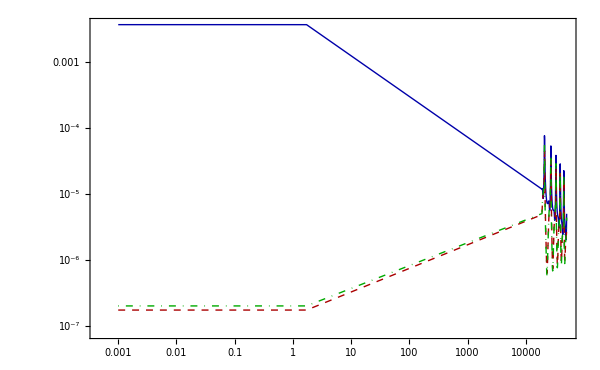

```mathematica
ListLogLogPlot[{Transpose@{freq, Abs[v1out[[All,4]]]},Transpose@{freq, Abs[v1out[[All,5]]]},Transpose@{freq, Abs[v1out[[All,6]]]}}, PlotRange->All]
```

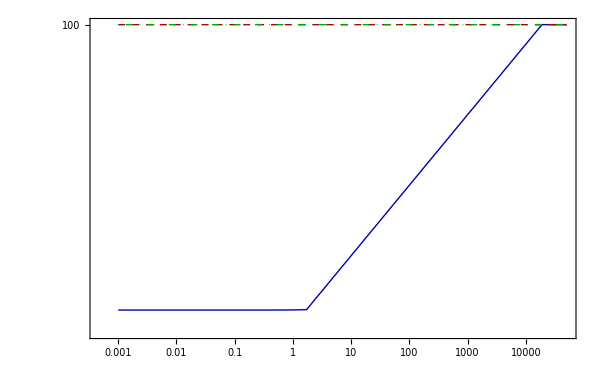

```mathematica
ListLogLogPlot[{Transpose@{freq, Abs[100-100v1out[[All,1]]]},Transpose@{freq, Abs[100-100v1out[[All,2]]]},Transpose@{freq, Abs[100-100v1out[[All,3]]]}}, PlotRange->All]
```